## Computing changes due to selection (M = 1)

First, we define the probability of imitation γ, fitness f_i, and average contribution of i ω_i for M = 1:

```mathematica
γ[n_,p_]:=1-(n*p)/(2(n-1))
(*makes[n_]:=Table[{Subscript[s, i,a],Subscript[s, i,d]},{i,1,n}]
makeh[n_]:=Table[Subscript[h, i],{i,1,n}]
(*quantities defined for convenience*)
splus[sarr_,i_]:=sarr[[i,1]]+sarr[[i,2]]
sminus[sarr_,i_]:=sarr[[i,1]]-sarr[[i,2]]*)
```

```mathematica
(*define payoff*)
payoff[i_]:=-Subscript[s, {i,a}](b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c (Subscript[s, {i,a}]+Subscript[s, {i,d}])+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l](Subscript[s, {i,a}]-Subscript[s, {i,d}])+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
(*define quantity shared among four strategies*)
Y[i_,n_]:=n*payoff[i]-∑_(j=1)^n payoff[j]//ExpandAll
Y[i,n]
```

-b n s_{i,a}+c n s_{i,a}+1/2 n ∑_(l=1)^n (-c s_{i,a}-c h_i h_l s_{i,a}-c s_{i,d}+c h_i h_l s_{i,d}+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})-∑_(j=1)^n (-(b-c) s_{j,a}+1/2 ∑_(l=1)^n (-c s_{j,a}-c h_j h_l s_{j,a}-c s_{j,d}+c h_j h_l s_{j,d}+b s_{l,a}+b h_j h_l s_{l,a}+b s_{l,d}-b h_j h_l s_{l,d}))

Next, we define some rules to simplify the summations:

```mathematica
(*rules for initial simplification*)
sumRule=Sum[expr1_,iter_]+Sum[expr2_,iter_]:>Sum[expr1+expr2,iter];
prodRule=Sum[expr1_,iter1_]*Sum[expr2_,iter2_]:>Sum[expr1*expr2,iter1,iter2];
revSumRule=Sum[expr1_+expr2_,iter_]:> Sum[expr1,iter]+Sum[expr2,iter];
constRule=Sum[c_?NumericQ expr_,iter_]:>c Sum[expr,iter];
distRule=a_(b_+c_):>a*b+a*c;
dist2Rule=s_Subscript(b_+c_):>s*b+s*c;

miscRule=s_Subscript Sum[expr_,iter_]:> Sum[s*expr,iter];
squareRule = s_Subscript^2:>s;
unbracketRule=Sum[expr_,{i_,1,n}]:> n expr;

(*rules for collecting terms*)
mergeRule=a_ s1_Subscript s2_Subscript+b_ s1_Subscript s2_Subscript:> (FullSimplify[a+b])s1 s2;
```

```mathematica
(*these quantities need to be multiplied by (1-p/2)(β/n^3)*)
expandBracket[bracket_]:=ExpandAll[bracket]/.revSumRule/.constRule/.distRule//.miscRule//.distRule //.squareRule//.sumRule//.unbracketRule

xCCbracket:=expandBracket[Subscript[s, {i,a}] Subscript[s, {i,d}] Y[i,n] ];
xCDbracket:=expandBracket[Subscript[s, {i,a}](1-Subscript[s, {i,d}])Y[i,n]] ;
xDCbracket:=expandBracket[(1-Subscript[s, {i,a}])Subscript[s, {i,d}] Y[i,n]]; 
xDDbracket:=expandBracket[(1-Subscript[s, {i,a}])(1-Subscript[s, {i,d}])Y[i,n]] ;
```

-b n s_{i,a} s_{i,d}+c n s_{i,a} s_{i,d}-1/2 c n^2 s_{i,a} s_{i,d}+n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 n^2 (-c s_{i,a} s_{i,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_i h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_i h_l s_{i,a} s_{i,d} s_{l,d})-1/2 n^2 (-c s_{i,a} s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,d}+c h_j h_l s_{i,a} s_{i,d} s_{j,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_j h_l s_{i,a} s_{i,d} s_{l,d})

```mathematica
(*attempt 3, CC*)
(*FullSimplify[xCDbracket]//.distRule*)
```

```mathematica
subCC1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCC2={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4(1/n+(n-1)/n y)};
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}] -> 1/4};
(*simplify*)
FullSimplify[xCCbracket]//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 // FullSimplify
```

1/4 (b+c (-1+n)) (-1+n) (-1+y)

```mathematica
(*attempt 3, DC*)
(*FullSimplify[xDCbracket]//.distRule*)
```

```mathematica
subDC5={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subDC6={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],(*duplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subDC7={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subDC8={Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y)};
subDC9={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,d}]->1/2};
(*simplify*)
FullSimplify[xDCbracket]//.distRule//.subDC5//.subDC6//.subDC7//.subDC8//.subDC9// FullSimplify
```

-1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

```mathematica
(*attempt 3, CD*)
(*FullSimplify[xDCbracket]//.distRule*)
```

```mathematica
subCD10={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCD11={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subCD12={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subCD13={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y)};
subCD14={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,a}]->1/2};
(*simplify*)
FullSimplify[xCDbracket]//.distRule//.subCD10//.subCD11//.subCD12//.subCD13//.subCD14//FullSimplify
```

1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

```mathematica
(*attempt 3, DD*)
(*FullSimplify[xDDbracket]//.distRule*)
```

```mathematica
(*we combine the simplifications from CD and DC*)
subDD15={Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y),
		Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4};
subDD16={Subscript[s, {j,a}]->1/2,Subscript[s, {j,d}]->1/2};
(*simplify*)
FullSimplify[xDDbracket]//.distRule//.subDC5//.subCD10//.subDC6//.subCD11//.subDC7//.subDD15//.subDD16//FullSimplify
```

-1/4 (b+c (-1+n)) (-1+n) (-1+y)

Thus, in summary, we have

```mathematica
xCCbracket2:=FullSimplify[xCCbracket]//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 // FullSimplify
xCDbracket2:=FullSimplify[xCDbracket]//.distRule//.subCD10//.subCD11//.subCD12//.subCD13//.subCD14//FullSimplify
xDCbracket2:=FullSimplify[xDCbracket]//.distRule//.subDC5//.subDC6//.subDC7//.subDC8//.subDC9// FullSimplify
xDDbracket2:=FullSimplify[xDDbracket]//.distRule//.subDC5//.subCD10//.subDC6//.subCD11//.subDC7//.subDD15//.subDD16//FullSimplify
```

```mathematica
Clear[nn,β,p,bb,cc,u,v];
ΔxCC[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xCCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxCD[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xCDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxDC[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xDCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxDD[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xDDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};

(*print quantities*)
ΔxCC[n,β,p,b,c,u,v]//FullSimplify
ΔxCD[n,β,p,b,c,u,v]//FullSimplify
ΔxDC[n,β,p,b,c,u,v]//FullSimplify
ΔxDD[n,β,p,b,c,u,v]//FullSimplify
```

((b+c (-1+n)) (-1+n) (-2+p) u β)/(16 n^2 (1+n u))

((-1+n) (-2+p) (9 (b+c (-1+n)) u (3+n u)^2+(b (72+n (-36-u (6+n u) (-31+11 n+n (-7+2 n) u)))+c (-72+n (36+u (6+n u) (-31+20 n+n (-7+5 n) u)))) v+n (c (-96+n (48+u (-91+50 n+n (-17+10 n) u)))+b (96+n (-48+u (91+n (-41+(17-7 n) u))))) v^2-(b-c) (-2+n) n^2 (12+5 n u) v^3) β)/(48 n^2 (3+n u) (1+n v) (3+n v) (1+n (u+v)) (3+n (u+v)))

-(((-1+n) (-2+p) (9 (b+c (-1+n)) u (3+n u)^2+(b (72+n (-36-u (6+n u) (-31+11 n+n (-7+2 n) u)))+c (-72+n (36+u (6+n u) (-31+20 n+n (-7+5 n) u)))) v+n (c (-96+n (48+u (-91+50 n+n (-17+10 n) u)))+b (96+n (-48+u (91+n (-41+(17-7 n) u))))) v^2-(b-c) (-2+n) n^2 (12+5 n u) v^3) β)/(48 n^2 (3+n u) (1+n v) (3+n v) (1+n (u+v)) (3+n (u+v))))

-((b+c (-1+n)) (-1+n) (-2+p) u β)/(16 n^2 (1+n u))

0.04

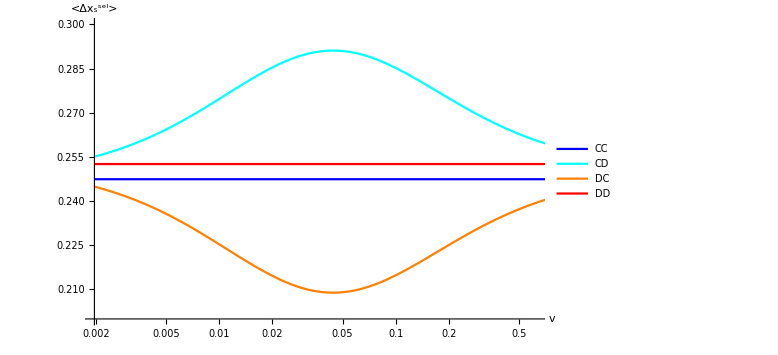

```mathematica
Clear[nn];
nn=40;uu=0.001;pp=0.0;ββ=0.0025;cc=0.2;bb=1.0;
factor1=1; factor2=1;
nn*uu*factor1

LogLinearPlot[{
1/4+(nn(1-uu))/uu ΔxCC[nn,ββ,pp,bb,cc,uu*factor1,v*factor2],
1/4+(nn(1-uu))/uu ΔxCD[nn,ββ,pp,bb,cc,uu*factor1,v*factor2],
1/4+(nn(1-uu))/uu ΔxDC[nn,ββ,pp,bb,cc,uu*factor1,v*factor2],
1/4+(nn(1-uu))/uu ΔxDD[nn,ββ,pp,bb,cc,uu*factor1,v*factor2]},{v,0,2},
AxesLabel->{"v","<Δx_s^sel>"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},{0.20,0.30}},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}]
```

```mathematica
Animate
```

```mathematica
(*attempt 2*)
(*checking values*)
FullSimplify[xCCbracket]//.distRule
```

-b n s_{i,a} s_{i,d}+c n s_{i,a} s_{i,d}-c n^2 s_{i,a} s_{i,d}+b n s_{i,a} s_{i,d} s_{j,a}-c n s_{i,a} s_{i,d} s_{j,a}+1/2 c n^2 s_{i,a} s_{i,d} s_{j,a}+1/2 c n^2 h_j h_l s_{i,a} s_{i,d} s_{j,a}+1/2 c n^2 s_{i,a} s_{i,d} s_{j,d}-1/2 c n^2 h_j h_l s_{i,a} s_{i,d} s_{j,d}+1/2 b n^2 h_i h_l s_{i,a} s_{i,d} s_{l,a}-1/2 b n^2 h_j h_l s_{i,a} s_{i,d} s_{l,a}-1/2 b n^2 h_i h_l s_{i,a} s_{i,d} s_{l,d}+1/2 b n^2 h_j h_l s_{i,a} s_{i,d} s_{l,d}

```mathematica
(*attempt 2*)
sub11={
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],(*duplet*)
Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]   (*duplet*)};
sub12={
Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4 Subscript[h, i] Subscript[h, l], (*<Subscript[s, {i,a}] Subscript[s, {i,d}]> is a constant that is independent of h's*)
Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4 Subscript[h, i] Subscript[h, l], (*<Subscript[s, {i,a}] Subscript[s, {l,d}]> is a constant that is independent of h's*)
Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4 Subscript[h, i] Subscript[h, l],
Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/4 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/4 Subscript[h, i] Subscript[h, l],
Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, j] Subscript[s, {i,a}] Subscript[s, {l,a}], (*using different pairs to distinguish patterns*)
Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> Subscript[h, i] Subscript[h, j] Subscript[s, {i,a}] Subscript[s, {l,a}],
Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2 Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
sub13={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2 Subscript[s, {j,a}] Subscript[s, {l,a}],(*<Subscript[s, {i,a}] Subscript[s, {i,d}]> is a constant that is independent of s_ja*)
	  Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2 Subscript[s, {j,a}] Subscript[s, {l,a}](*w.l.o.g., we use the 'a' strategy as the common strategy*)};
sub14={ Subscript[s, {i,a}] Subscript[s, {j,d}]->1/4,Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,	  
Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {j,a}] Subscript[s, {l,a}],
Subscript[s, {i,a}] Subscript[s, {j,a}]-> Subscript[s, {j,a}] Subscript[s, {l,a}],	  
Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l] ,
Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l] ,
Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l]
};
(*finally, substitute y, z, g, h*)
sub15={ Subscript[s, {j,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n y)(*y*), Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z(*z*), Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g)(*g*),
Subscript[h, i] Subscript[h, j] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y)) (*h*)};
sub16={Subscript[s, {i,a}]-> 1/2,Subscript[s, {i,d}]-> 1/2,Subscript[s, {j,a}]-> 1/2,Subscript[s, {j,d}]-> 1/2};
```

```mathematica
FullSimplify[xCCbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
FullSimplify[xCDbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
FullSimplify[xDCbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
FullSimplify[xDDbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
```

1/4 (b+c (-1+n)) (-1+n) (-1+y)

1/16 (b (-8-4 g (-1+n)-4 h (-2+n) (-1+n)+5 n+8 y-8 n y+4 z+(-5+n) n z)+c (4-4 y+n (-1+4 y+3 (-1+n) z)))

1/16 (b (8+4 g (-1+n)+4 h (-2+n) (-1+n)-5 n-8 y+8 n y-(-4+n) (-1+n) z)+2 c (-2+n+2 y-2 n y-(-1+n) n z))

1/16 (4 b (-1+n+y-n y)+c (4-4 y+n (-9+8 y+z-n (-4+4 y+z))))

```mathematica
xCCbracket2:=FullSimplify[xCCbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
xCDbracket2:=FullSimplify[xCDbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
xDCbracket2:=FullSimplify[xDCbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
xDDbracket2:=FullSimplify[xDDbracket]//.distRule//.sub11//.sub12//.sub13//.sub14//.sub15//.sub16//FullSimplify
```

```mathematica
ΔxCC[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xCCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxCD[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xCDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxDC[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xDCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxDD[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xDDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};

ΔxCC[n,β,p,b,c,u,v]
ΔxCD[n,β,p,b,c,u,v]
ΔxDC[n,β,p,b,c,u,v]
ΔxDD[n,β,p,b,c,u,v]
```

((b+c (-1+n)) (-1+n) (1-p/2) (-1+(2+n u)/(2+2 n u)) β)/(4 n^3)

1/(16 n^3)(1-p/2) (c (4-(4 (2+n u))/(2+2 n u)+n (-1+(4 (2+n u))/(2+2 n u)+(3 (-1+n))/(1+n v)))+b (-8+5 n+(8 (2+n u))/(2+2 n u)-(8 n (2+n u))/(2+2 n u)+4/(1+n v)+((-5+n) n)/(1+n v)-4 (-2+n) (-1+n) ((11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v)))-2 (-1+n) (1/(1+n v)+1/(1+n (u+v))))) β

1/(16 n^3)(1-p/2) (2 c (-2+n+(2 (2+n u))/(2+2 n u)-(2 n (2+n u))/(2+2 n u)-((-1+n) n)/(1+n v))+b (8-5 n-(8 (2+n u))/(2+2 n u)+(8 n (2+n u))/(2+2 n u)-((-4+n) (-1+n))/(1+n v)+4 (-2+n) (-1+n) ((11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v)))+2 (-1+n) (1/(1+n v)+1/(1+n (u+v))))) β

((1-p/2) (4 b (-1+n+(2+n u)/(2+2 n u)-(n (2+n u))/(2+2 n u))+c (4-(4 (2+n u))/(2+2 n u)+n (-9+(8 (2+n u))/(2+2 n u)+1/(1+n v)-n (-4+(4 (2+n u))/(2+2 n u)+1/(1+n v))))) β)/(16 n^3)

```mathematica
ΔxCC[40,0.001,0,1.0,0.2,0.001,v]
ΔxCD[40,0.001,0,1.0,0.2,0.001,v]
ΔxDC[40,0.001,0,1.0,0.2,0.001,v]
ΔxDD[40,0.001,0,1.0,0.2,0.001,v]
```

-2.57813×10^-8

9.76563×10^-10 (0.2 (0.0769231+40 (2.92308+117/(1+40 v)))+1. (-114.+1404/(1+40 v)-5928 (0.911765/(1+40 v)+0.414474/(1.04+40 v)-1/(2 (3+40 v))-0.495098/(3.04+40 v))-78 (1/(1+40 v)+1/(1+40 (0.001+v)))))

9.76563×10^-10 (0.4 (-38.5-1560/(1+40 v))+1. (114.-1404/(1+40 v)+5928 (0.911765/(1+40 v)+0.414474/(1.04+40 v)-1/(2 (3+40 v))-0.495098/(3.04+40 v))+78 (1/(1+40 v)+1/(1+40 (0.001+v)))))

9.76563×10^-10 (3.+0.2 (0.0769231+40 (-1.15385+1/(1+40 v)-40 (-0.0769231+1/(1+40 v)))))

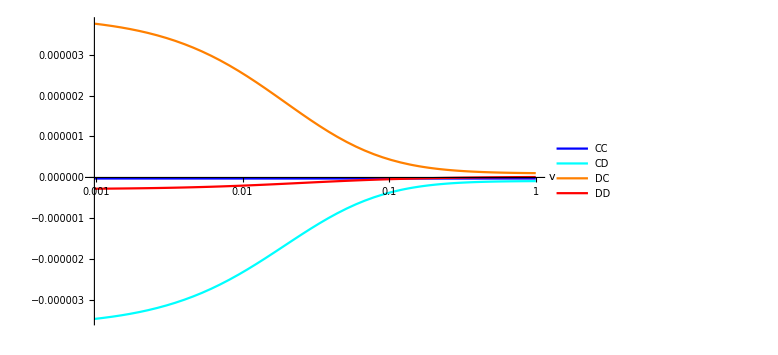

```mathematica
LogLinearPlot[{
ΔxCC[40,0.001,0,1.0,0.2,0.001,v],
ΔxCD[40,0.001,0,1.0,0.2,0.001,v],
ΔxDC[40,0.001,0,1.0,0.2,0.001,v],
ΔxDD[40,0.001,0,1.0,0.2,0.001,v]},{v,0,1},
AxesLabel->Automatic,PlotLegends->{"CC","CD","DC","DD"},ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}]
```

```mathematica
(*previous calculation*)
(*make substitutions for terms that go away when we take averages; substitution order matters*)
sub1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
	Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
sub2={ Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],
         Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}],
	Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]};
sub3 ={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
	Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };

(*taking brackets via substitution*)
sub4={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2 Subscript[s, {i,a}] Subscript[s, {j,a}]}; (*<Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]=1/2<Subscript[s, {i,a}] Subscript[s, {j,a}]> because Subscript[s, {i,a}]& Subscript[s, {i,d}] and Subscript[s, {i,d}]& Subscript[s, {j,a}] are independent*)
sub5={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4 Subscript[h, i] Subscript[h, l]};
(*careful with the timing of the next sub*)
sub6={Subscript[s, {i,d}] Subscript[s, {j,a}]-> Subscript[s, {i,a}] Subscript[s, {j,d}]};

(*finally, substitute y, g, z, h*)
sub7={ Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
	Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4(1/n+(n-1)/n z),
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4(1/n+(n-1)/n z),
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y)),
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
sub8={ Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n z),Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2(1/n+(n-1)/n z),
	Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n z),Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n z),
	Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2(1/n+(n-1)/n z),Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n z),
	Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2(1/n+(n-1)/n z)};
sub9={ Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,
	Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y),
	Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4, Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4};
sub10={Subscript[s, {i,a}]-> 1/2,Subscript[s, {i,d}]-> 1/2,Subscript[s, {j,a}]-> 1/2,Subscript[s, {j,d}]-> 1/2};
```

```mathematica
xCCbracket2:=FullSimplify[xCCbracket]//.distRule//.sub1//.sub2//.sub3//.sub4//.sub5//.sub6//.sub7//.sub8//.sub9//.sub10//FullSimplify
xCDbracket2:=FullSimplify[xCDbracket]//.distRule//.sub1//.sub2//.sub3//.sub4//.sub5//.sub6//.sub7//.sub8//.sub9//.sub10//FullSimplify
xDCbracket2:=FullSimplify[xDCbracket]//.distRule//.sub1//.sub2//.sub3//.sub4//.sub5//.sub6//.sub7//.sub8//.sub9//.sub10//FullSimplify
xDDbracket2:=FullSimplify[xDDbracket]//.distRule//.sub1//.sub2//.sub3//.sub4//.sub5//.sub6//.sub7//.sub8//.sub9//.sub10//FullSimplify
```

```mathematica
ΔxCC[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xCCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxCD[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xCDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxDC[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xDCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};
ΔxDD[nn_,β_,p_,bb_,cc_,u_,v_]=(1-p/2)(β/nn^3)*xDDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc[nn,u,v],z-> zcalc[nn,u,v],g-> gcalc[nn,u,v],h-> hcalc[nn,u,v]};

ΔxCC[n,β,p,b,c,u,v]
ΔxCD[n,β,p,b,c,u,v]
ΔxDC[n,β,p,b,c,u,v]
ΔxDD[n,β,p,b,c,u,v]
```

((b+c (-1+n)) (-1+n) (1-p/2) (-1+(2+n u)/(2+2 n u)) β)/(4 n^3)

-1/(4 n^3)(-1+n) (1-p/2) (c (1/(1+n v)-n/(1+n v)+(-2+n) ((11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v)))+1/2 (1/(1+n v)+1/(1+n (u+v))))-b (1/(1+n v)+(-2+n) ((11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v)))+1/2 (1/(1+n v)+1/(1+n (u+v)))-1/2 n (1/(1+n v)+1/(1+n (u+v))))) β

1/(4 n^3)(-1+n) (1-p/2) (c (1/(1+n v)-n/(1+n v)+(-2+n) ((11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v)))+1/2 (1/(1+n v)+1/(1+n (u+v))))-b (1/(1+n v)+(-2+n) ((11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v)))+1/2 (1/(1+n v)+1/(1+n (u+v)))-1/2 n (1/(1+n v)+1/(1+n (u+v))))) β

-((b+c (-1+n)) (-1+n) (1-p/2) (-1+(2+n u)/(2+2 n u)) β)/(4 n^3)

```mathematica
ΔxCC[40,0.001,0,1.0,0.2,0.001,v]
ΔxCD[40,0.001,0,1.0,0.2,0.001,v]
ΔxDC[40,0.001,0,1.0,0.2,0.001,v]
ΔxDD[40,0.001,0,1.0,0.2,0.001,v]
```

-2.57813×10^-8

-1.52344×10^-7 (-1. (1/(1+40 v)+38 (0.911765/(1+40 v)+0.414474/(1.04+40 v)-1/(2 (3+40 v))-0.495098/(3.04+40 v))-39/2 (1/(1+40 v)+1/(1+40 (0.001+v))))+0.2 (-39/(1+40 v)+38 (0.911765/(1+40 v)+0.414474/(1.04+40 v)-1/(2 (3+40 v))-0.495098/(3.04+40 v))+1/2 (1/(1+40 v)+1/(1+40 (0.001+v)))))

1.52344×10^-7 (-1. (1/(1+40 v)+38 (0.911765/(1+40 v)+0.414474/(1.04+40 v)-1/(2 (3+40 v))-0.495098/(3.04+40 v))-39/2 (1/(1+40 v)+1/(1+40 (0.001+v))))+0.2 (-39/(1+40 v)+38 (0.911765/(1+40 v)+0.414474/(1.04+40 v)-1/(2 (3+40 v))-0.495098/(3.04+40 v))+1/2 (1/(1+40 v)+1/(1+40 (0.001+v)))))

2.57813×10^-8

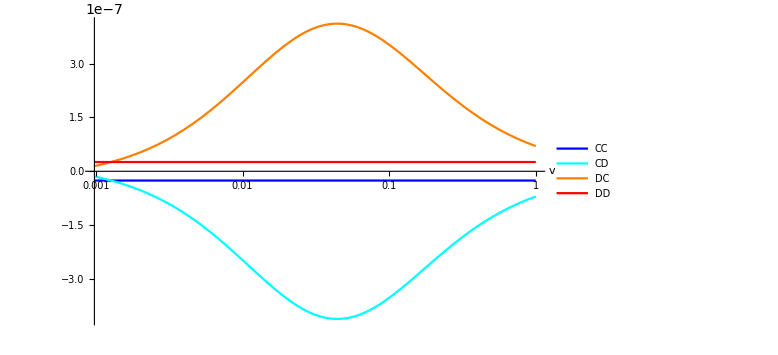

```mathematica
LogLinearPlot[{
ΔxCC[40,0.001,0,1.0,0.2,0.001,v],
ΔxCD[40,0.001,0,1.0,0.2,0.001,v],
ΔxDC[40,0.001,0,1.0,0.2,0.001,v],
ΔxDD[40,0.001,0,1.0,0.2,0.001,v]},{v,0,1},
AxesLabel->Automatic,PlotLegends->{"CC","CD","DC","DD"},ImageSize->Large,PlotStyle->{Blue,Cyan,Orange,Red}]
```

```mathematica
(*(*make substitutions for terms that go away when we take averages; substitution order matters*)
sub1={Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
	Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
sub2={Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],
         Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}],
	Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}],
	Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]};
sub3 ={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
	Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };*)

(*intermediate results*)
xCCbracket/.sub1/.sub2/.sub3
xCDbracket/.sub1/.sub2/.sub3
xDCbracket/.sub1/.sub2/.sub3
xDDbracket/.sub1/.sub2/.sub3
```

-b n s_{i,a} s_{i,d}+c n s_{i,a} s_{i,d}-1/2 c n^2 s_{i,a} s_{i,d}+n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 n^2 (-c s_{i,a} s_{i,d}+2 b s_{i,a} s_{i,d} s_{l,a})-1/2 n^2 (-2 c s_{i,a} s_{i,d} s_{j,a}+2 b s_{i,a} s_{i,d} s_{l,a})

n (b s_{i,d} s_{j,a}-c s_{i,d} s_{j,a})-n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})-1/2 n^2 (-c s_{i,a} s_{i,d}+2 b s_{i,a} s_{i,d} s_{l,a})+1/2 n^2 (-2 c s_{i,a} s_{i,d} s_{j,a}+2 b s_{i,a} s_{i,d} s_{l,a})+1/2 n^2 (-c s_{i,d}+c h_i h_l s_{i,d}-c h_i h_l s_{i,a} s_{i,d}-b h_i h_l s_{i,a} s_{l,a}+b s_{i,d} s_{l,a}+b h_i h_l s_{i,a} s_{l,d}+b s_{i,d} s_{l,d})-1/2 n^2 (c h_j h_l s_{i,a} s_{j,a}-c s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{j,d}-c s_{i,d} s_{j,d}-b h_j h_l s_{i,a} s_{l,a}+b s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{l,d}+b s_{i,d} s_{l,d})

-b n s_{i,a}+c n s_{i,a}-1/2 c n^2 s_{i,a}+b n s_{i,a} s_{i,d}-c n s_{i,a} s_{i,d}+1/2 c n^2 s_{i,a} s_{i,d}+n (b s_{i,a} s_{j,a}-c s_{i,a} s_{j,a})-n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})-1/2 n^2 (-c s_{i,a} s_{i,d}+2 b s_{i,a} s_{i,d} s_{l,a})+1/2 n^2 (-2 c s_{i,a} s_{i,d} s_{j,a}+2 b s_{i,a} s_{i,d} s_{l,a})-1/2 n^2 (-c s_{i,a} s_{j,a}-c h_j h_l s_{i,a} s_{j,a}-c s_{i,a} s_{j,d}-b h_j h_l s_{i,a} s_{j,d}+c h_j h_l s_{i,a} s_{j,d}+b s_{i,a} s_{l,a}+b h_j h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d})+1/2 n^2 (-c h_i h_l s_{i,a}-c s_{i,a} s_{i,d}+c h_i h_l s_{i,a} s_{i,d}+b s_{i,a} s_{l,a}+b h_i h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d}-b h_i h_l s_{i,a} s_{l,d})

-n (b s_{i,a} s_{j,a}-c s_{i,a} s_{j,a})-n (b s_{i,d} s_{j,a}-c s_{i,d} s_{j,a})+n (b s_{j,a}-c s_{j,a}+b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 n^2 (-c s_{i,a} s_{i,d}+2 b s_{i,a} s_{i,d} s_{l,a})-1/2 n^2 (-2 c s_{i,a} s_{i,d} s_{j,a}+2 b s_{i,a} s_{i,d} s_{l,a})+1/2 n^2 (-c h_i h_l s_{i,a}-c s_{i,d}+c h_i h_l s_{i,d}+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})-1/2 n^2 (-c s_{j,a}-c h_j h_l s_{j,a}-c s_{j,d}+c h_j h_l s_{j,d}+b s_{l,a}+b h_j h_l s_{l,a}+b s_{l,d}-b h_j h_l s_{l,d})+1/2 n^2 (-c s_{i,a} s_{j,a}-c h_j h_l s_{i,a} s_{j,a}-c s_{i,a} s_{j,d}-b h_j h_l s_{i,a} s_{j,d}+c h_j h_l s_{i,a} s_{j,d}+b s_{i,a} s_{l,a}+b h_j h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d})-1/2 n^2 (-c h_i h_l s_{i,a}-c s_{i,a} s_{i,d}+c h_i h_l s_{i,a} s_{i,d}+b s_{i,a} s_{l,a}+b h_i h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d}-b h_i h_l s_{i,a} s_{l,d})-1/2 n^2 (-c s_{i,d}+c h_i h_l s_{i,d}-c h_i h_l s_{i,a} s_{i,d}-b h_i h_l s_{i,a} s_{l,a}+b s_{i,d} s_{l,a}+b h_i h_l s_{i,a} s_{l,d}+b s_{i,d} s_{l,d})+1/2 n^2 (c h_j h_l s_{i,a} s_{j,a}-c s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{j,d}-c s_{i,d} s_{j,d}-b h_j h_l s_{i,a} s_{l,a}+b s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{l,d}+b s_{i,d} s_{l,d})

```mathematica
(*taking brackets via substitution*)
sub5={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2 Subscript[s, {i,a}] Subscript[s, {j,a}],Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 Subscript[s, {i,a}] Subscript[s, {l,a}]}; (*<Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]=1/2<Subscript[s, {i,a}] Subscript[s, {j,a}]> because Subscript[s, {i,a}]& Subscript[s, {i,d}] and Subscript[s, {i,d}]& Subscript[s, {j,a}] are independent*)
sub6={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4 Subscript[h, i] Subscript[h, l]};
FullSimplify[xCCbracket/.sub1/.sub2/.sub3/.sub4/.sub5/.sub6]//.distRule
FullSimplify[xCDbracket/.sub1/.sub2/.sub3/.sub4/.sub5/.sub6]//.distRule
FullSimplify[xDCbracket/.sub1/.sub2/.sub3/.sub4/.sub5/.sub6]//.distRule
FullSimplify[xDDbracket/.sub1/.sub2/.sub3/.sub4/.sub5/.sub6]//.distRule
```

-b n s_{i,a} s_{i,d}+c n s_{i,a} s_{i,d}-c n^2 s_{i,a} s_{i,d}+1/2 b n s_{i,a} s_{j,a}-1/2 c n s_{i,a} s_{j,a}+1/2 c n^2 s_{i,a} s_{j,a}

-1/8 c n^2 h_i h_l-1/2 c n^2 s_{i,d}+1/2 c n^2 h_i h_l s_{i,d}+1/2 c n^2 s_{i,a} s_{i,d}-1/2 b n s_{i,a} s_{j,a}+1/2 c n s_{i,a} s_{j,a}+b n s_{i,d} s_{j,a}-c n s_{i,d} s_{j,a}+1/2 c n^2 s_{i,d} s_{j,a}

1/8 c n^2 h_i h_l-b n s_{i,a}+c n s_{i,a}-1/2 c n^2 s_{i,a}-1/2 c n^2 h_i h_l s_{i,a}+b n s_{i,a} s_{i,d}-c n s_{i,a} s_{i,d}+1/2 c n^2 s_{i,a} s_{i,d}+1/2 b n s_{i,a} s_{j,a}-1/2 c n s_{i,a} s_{j,a}+1/2 b n^2 h_j h_l s_{i,a} s_{j,a}+1/2 c n^2 s_{i,a} s_{j,d}-1/2 b n^2 h_j h_l s_{i,a} s_{l,a}

b n s_{j,a}-c n s_{j,a}+1/2 c n^2 s_{j,a}-1/2 b n s_{i,a} s_{j,a}+1/2 c n s_{i,a} s_{j,a}-1/2 c n^2 s_{i,a} s_{j,a}-1/2 b n^2 h_j h_l s_{i,a} s_{j,a}-b n s_{i,d} s_{j,a}+c n s_{i,d} s_{j,a}-1/2 c n^2 s_{i,d} s_{j,a}+1/2 c n^2 s_{j,d}-1/2 c n^2 s_{i,a} s_{j,d}+1/2 b n^2 h_j h_l s_{i,a} s_{l,a}

## Computing y

```mathematica
γ[n_,p_]:=1-(n*p)/(2(n-1))
tt[τ_,n_,p_]:=τ*(n^2/(2γ[n,p]))
ρ[τ_,p_]:=Exp[-τ]
ρ2[τ3_,τ2_]:=3*Exp[-3*τ3]Exp[-τ2]
```

```mathematica
(*Check manual derivation of γ*)
(1*(n/2-1)/(n-1)+(1-p)*(n/2)/(n-1))- γ[n,p] == 0// FullSimplify
```

True

```mathematica
(*Check the manual derivation of y(τ)*)
yt[t_,n_,p_,u_]:=1/2(1+(1-u/n γ[n,p])^(2*t))
yt[tt[τ,n,p],n,p,μ/n];
(*take the limit after replacing t=τ*(n^2/(2(1-p/2))) and u=μ/n*)
ytau[μ_,τ_,p_]:=Limit[yt[tt[τ,n,p],n,p,μ/n],n->Infinity]
ytau[μ,τ,p]
```

1/2 (1+ⅇ^(-μ τ))

```mathematica
(*Check the integration of y*)
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
yeval[μ_,ν_]=y[μ,p];
ycalc[n_,u_,v_]=y[μ,p]/.{μ->n*u};
```

```mathematica
yeval[μ,ν]
ycalc[n,u,v]
```

(2+μ)/(2+2 μ)

(2+n u)/(2+2 n u)

## Computing z

```mathematica
(*Check what happens if we change to τ=t/(n^2/2γ), μ=νu *)
zt[t_,n_,p_,v_]:=(1-v/n γ[n,p])^(2*t)
(*take the limit after replacing t=τ*(n^2/(2γ)) and v=ν/n)*)
ztau[ν_,τ_,p_]:=Limit[zt[tt[τ,n,p],n,p,ν/n],n->Infinity]
ztau[ν,τ,p]
```

ⅇ^(-ν τ)

```mathematica
(*Check integration with τ=t/(n^2/2γ)*)
z[ν_,p_]:=Integrate[ztau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
zeval[μ_,ν_]=z[ν,p]// FullSimplify;
zcalc[n_,u_,v_]=z[ν,p]/.{ν->n*v} // FullSimplify;
```

```mathematica
zeval[μ,ν]
zcalc[n,u,v]
```

1/(1+ν)

1/(1+n v)

## Computing g

```mathematica
(*Check what happens if we change to τ=t/(n^2/2γ), μ=nu *)
gtau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*ztau[ν,τ,p]
gtau[μ,ν,τ,p]
```

1/2 ⅇ^(-ν τ) (1+ⅇ^(-μ τ))

```mathematica
(*Check integration with τ=t/(n^2/2γ)*)
g[μ_,ν_,p_]:=Integrate[gtau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
geval[μ_,ν_]=g[μ,ν,p] // FullSimplify;
gcalc[n_,u_,v_]=g[μ,ν,p]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
geval[μ,ν](*check*)
gcalc[n,u,v](*check*)
```

1/2 (1/(1+ν)+1/(1+μ+ν))

1/2 (1/(1+n v)+1/(1+n (u+v)))

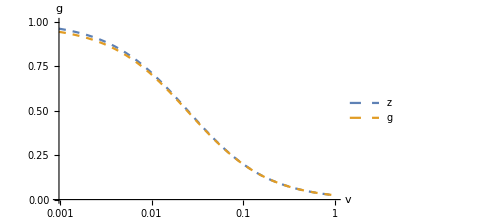

```mathematica
params={β->0.001,u->0.001,n->40};
LogLinearPlot[{zcalc[n,u,v]/.params,gcalc[n,u,v]/.params},{v,0,1},PlotRange->{0,1},AxesLabel->{"v","g"},PlotLegends->Placed[{"z","g"},{0.9,0.5}],ImageSize->Medium,PlotStyle->Dashed]
(*these functions are different but the difference is smalll when u is small*)
```

## Computing h

```mathematica
htau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*ztau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3+τ2,p])
h[μ_,ν_,p_]:=Integrate[htau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ2,0,Infinity},{τ3,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
hcalc[n_,u_,v_]=h[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
heval[μ_,ν_]=h[μ,ν,p] // FullSimplify//Apart;
```

```mathematica
hcalc[n,u,v]
heval[μ,ν]
```

(11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v))

(11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν))

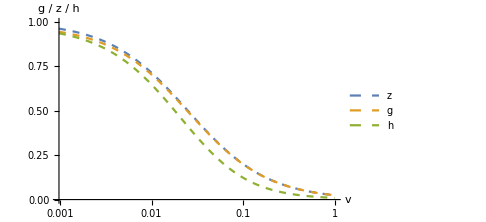

```mathematica
(*plot all three quantities: g, y, *)
params={β->0.001,u->0.001,n->40};
expressions={ zcalc[n,u,v](*z*) ,gcalc[n,u,v](*g*), hcalc[n,u,v](*h*)}/.params;
LogLinearPlot[expressions,{v,0,1},PlotRange->{0,1},AxesLabel->{"v","g / z / h"},PlotLegends->Placed[{z,g,h},{0.9,0.5}],ImageSize->Medium,PlotStyle->Dashed]
```

## Compute theoretical predictions and export data

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];
(*ps =Table[p,{p,0,1,0.25}];*) (*we know that y, z, g, h is independent of p*)
(*compute y,z,g,h for each (u,v) pair*)
data=Flatten[
Table[{u/.params,v,ycalc[n,u,v]/.params,
zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv";
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv

```mathematica
data // MatrixForm
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.935249
0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.914037
0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.883833
0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.841773
0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.784999
0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.711551
0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.621685
0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.519158
0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.411507
0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.308473
0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.218936
0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.148079
0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.0965029
0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.0614246
0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0386959
0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0243834
0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0154707)

```mathematica
data//MatrixForm (*exported data*)
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.935249
0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.914037
0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.883833
0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.841773
0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.784999
0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.711551
0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.621685
0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.519158
0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.411507
0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.308473
0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.218936
0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.148079
0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.0965029
0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.0614246
0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0386959
0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0243834
0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0154707)

```mathematica
(*printing expresisons to be included in SI*)
FullSimplify[Apart[ycalc[n,u,v]]/.{n*u->μ,n*v->ν}]
FullSimplify[Apart[zcalc[n,u,v]]/.{n*u->μ,n*v->ν}]
FullSimplify[Apart[gcalc[n,u,v]]/.{n*u->μ,n*v->ν}]
FullSimplify[Apart[hcalc[n,u,v]]/.{n*u->μ,n*v->ν}](*the FullSimplify is just for formatting*)
```

(2+μ)/(2+2 μ)

1/(1+ν)

1/2 (1/(1+ν)+1/(1+μ+ν))

1/12 (-6/(3+ν)+(3 (5+μ))/((3+μ) (1+μ+ν))-(3 (4+μ))/((2+μ) (3+μ+ν))+(22+8 μ)/(2+μ+2 ν+μ ν))

## Compute changes due to selection

```mathematica
(*compute the larger brackets*)
sasdY[n_,b_,c_,u_,v_]:=n^2*(-(b-c)-c*n)*(1/4-1/4(1/n+(n-1)/n ycalc[n,u,v]));
saY[n_,b_,c_,u_,v_]:=n^2*(
(-(b-c)-1/2 c n)*1/2(1-(1/n+(n-1)/n ycalc[n,u,v]))
-1/2 c n*3/4(1/n+(n-1)/n zcalc[n,u,v])+1/2 c n*1/4(1/n+(n-1)/n zcalc[n,u,v])+1/2 b n*1/2(1/n+(n-1)/n gcalc[n,u,v])
-1/2(b-c)n*(1/n^2+((n-1)(n-2))/n^2 hcalc[n,u,v]+(n-1)/n^2(zcalc[n,u,v]+gcalc[n,u,v]+ycalc[n,u,v]))
);
sdY[n_,b_,c_,u_,v_]:=-1/4 c n^3((n-1)/n(1-ycalc[n,u,v])-(1/n+(n-1)/n zcalc[n,u,v]))+ 1/4 b n^3(1/n+(n-1)/n gcalc[n,u,v])+1/4(b-c)n^3(1/n^2+((n-1)(n-2))/n^2 hcalc[n,u,v]+(n-1)/n^2(zcalc[n,u,v]+gcalc[n,u,v]+ycalc[n,u,v]));
```

```mathematica
ΔxCC[n_,β_,p_,b_,c_,u_,v_]:=β/n^2(1-p/2)(sasdY[n,b,c,u,v])
ΔxCD[n_,β_,p_,b_,c_,u_,v_]:=β/n^2(1-p/2)(saY[n,b,c,u,v]-sasdY[n,b,c,u,v])
ΔxDC[n_,β_,p_,b_,c_,u_,v_]:=β/n^2(1-p/2)(sdY[n,b,c,u,v]-sasdY[n,b,c,u,v])
ΔxDD[n_,β_,p_,b_,c_,u_,v_]:=β/n^2(1-p/2)(sasdY[n,b,c,u,v]-saY[n,b,c,u,v]-sdY[n,b,c,u,v])
```

```mathematica
(*compute change due to selection*)
params={p->0};
ΔxCC[40,0.001,p,1.0,0.2,0.001,v]/.params//N//FullSimplify
ΔxCD[40,0.001,p,1.0,0.2,0.001,v]/.params//N//FullSimplify
ΔxDC[40,0.001,p,1.0,0.2,0.001,v]/.params//N//FullSimplify
ΔxDD[40,0.001,p,1.0,0.2,0.001,v]/.params//N//FullSimplify
```

-0.00004125

(-2.92371×10^-8+v (-1.45206×10^-6+v (-0.0000119908+(0.00001317-0.00019625 v) v)))/(3.705×10^-6+v (0.00038885+v (0.014051+v (0.202+1. v))))

(7.28635×10^-8+v (4.60883×10^-6+v (0.0000804893+(0.000464594+0.0005 v) v)))/(3.705×10^-6+v (0.00038885+v (0.014051+v (0.202+1. v))))

(-4.34735×10^-8+v (-3.14073×10^-6+v (-0.0000679189+(-0.000469431-0.0002625 v) v)))/(3.705×10^-6+v (0.00038885+v (0.014051+v (0.202+1. v))))

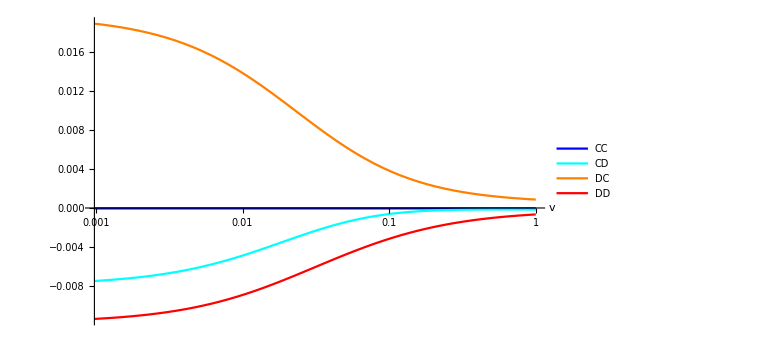

```mathematica
LogLinearPlot[{
ΔxCC[40,0.001,0,1.0,0.2,0.001,v],
ΔxCD[40,0.001,0,1.0,0.2,0.001,v],
ΔxDC[40,0.001,0,1.0,0.2,0.001,v],
ΔxDD[40,0.001,0,1.0,0.2,0.001,v]},{v,0,1},
AxesLabel->Automatic,PlotLegends->{"CC","CD","DC","DD"},ImageSize->Large,PlotStyle->{Blue,Cyan,Orange,Red}]
```

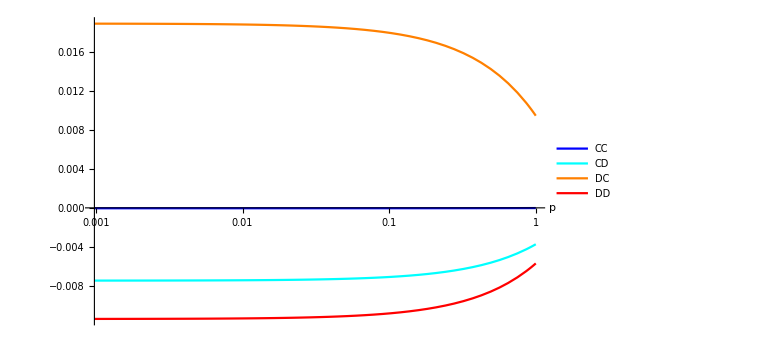

```mathematica
vv=0.001;
LogLinearPlot[{
ΔxCC[40,0.001,p,1.0,0.2,0.001,vv],
ΔxCD[40,0.001,p,1.0,0.2,0.001,vv],
ΔxDC[40,0.001,p,1.0,0.2,0.001,vv],
ΔxDD[40,0.001,p,1.0,0.2,0.001,vv]},{p,0,1},
AxesLabel->Automatic,PlotLegends->{"CC","CD","DC","DD"},ImageSize->Large,PlotStyle->{Blue,Cyan,Orange,Red}]
```